### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
{timeHdata,d2eH}=AbsoluteTiming@D2E[Data/.{I1-> 20,I2->20, U1-> 20,U2->10,U3->0}];
timeHdata;
{timeH,{systemH,rulesH}}=AbsoluteTiming@CriticalCongestionSolver[d2eH];
timeH
```

6.56329

```mathematica
alpha=1;
{timeHs,rulesHs}=AbsoluteTiming@Solver[d2eH][1];
timeHs
```

The error (1-Norm of LHS-RHS) is 1.59289×10^-13

The error is 1.59289×10^-13 which is less than 1.×10^-10

It took 6.66207 seconds to solve!
	The system is True

6.66362

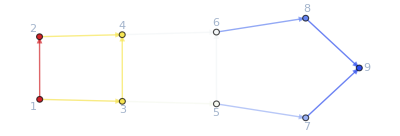

```mathematica
ColorNetworkByValueFunctionOperator[d2eH][rulesH]
```

```mathematica
{timeheterodata,d2ehetero}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timeheterodata;
{timehetero,{systemhetero,resulthetero}}=AbsoluteTiming@CriticalCongestionSolver[d2ehetero];
timehetero
```

j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j26+j8-jt37-jt39≥0&&j12≥0&&j28+j9-jt43-jt45≥0&&j14≥0&&j17≥0&&-j10+j2+j20+j23+j27-j4-j7-j8+jt37+jt39≥0&&-j12-j20-j23+j29+j3+j4+j7-j9+jt43+jt45≥0&&j20≥0&&-j10+j23+j27+j5-j7-j8+jt37+jt39≥0&&-j12-j23+j29+j6+j7-j9+jt43+jt45≥0&&j23≥0&&-j10+j27+jt37+jt39≥0&&-j12+j29+jt43+jt45≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&-j10-j12+j14+j26+j28≥0&&1-j1-j10+j17+j20+j23+j27-j4-j7-j8+jt37+jt39≥0&&2+j1-j12-j17-j20-j23+j29+j4+j7-j9+jt43+jt45≥0&&jt1≥0&&j17-jt1≥0&&-1+j1+j2-jt1≥0&&1-j1-j10+j20+j23+j27-j4-j7-j8+jt1+jt37+jt39≥0&&1-j2+jt1≥0&&j2-jt1≥0&&j3-jt12≥0&&j1-j3+jt12≥0&&-2+j17+jt12≥0&&2-j12-j17-j20-j23+j29+j3+j4+j7-j9-jt12+jt43+jt45≥0&&2-jt12≥0&&jt12≥0&&j2-jt14≥0&&jt14≥0&&j20-j5+jt14≥0&&j5-jt14≥0&&-j10+j2+j23+j27-j4+j5-j7-j8-jt14+jt37+jt39≥0&&-j2+j4+jt14≥0&&j3-jt20≥0&&jt20≥0&&j4-j6+jt20≥0&&j6-jt20≥0&&-j12-j20-j23+j29+j3+j6+j7-j9-jt20+jt43+jt45≥0&&j20-j3+jt20≥0&&j5-jt26≥0&&jt26≥0&&j23-j8+jt26≥0&&j8-jt26≥0&&-j10+j27+j5-j7-jt26+jt37+jt39≥0&&-j5+j7+jt26≥0&&j6-jt32≥0&&jt32≥0&&j7-j9+jt32≥0&&j9-jt32≥0&&-j12-j23+j29+j6-jt32+jt43+jt45≥0&&j23-j6+jt32≥0&&jt37≥0&&j8-jt37≥0&&jt39≥0&&j26-jt39≥0&&-j10+j27+jt37≥0&&j10-jt37≥0&&jt43≥0&&j9-jt43≥0&&jt45≥0&&j28-jt45≥0&&-j12+j29+jt43≥0&&j12-jt43≥0&&j10-jt50≥0&&jt50≥0&&j12-j14+jt50≥0&&j14-jt50≥0&&-j12+j14+j26-jt50≥0&&-j10+j28+jt50≥0&&j10-j20-j23-j27+j4+j7+j8-jt37-jt39+u18≥u15&&u1==j10-j20-j23-j27+j4+j7+j8-jt37-jt39+u18&&j12+j20+j23-j29-j4-j7+j9-jt43-jt45+u19≥u16&&-j1+j17+u1==j12+j20+j23-j29-j4-j7+j9-jt43-jt45+u19&&-j20+j4+u20==j10-j23-j27+j7+j8-jt37-jt39+u21&&u18==j10-j23-j27+j7+j8-jt37-jt39+u21&&u20==j12+j23-j29-j7+j9-jt43-jt45+u22&&u19==j12+j23-j29-j7+j9-jt43-jt45+u22&&-j23+j7+u23==j10-j27+j8-jt37-jt39+u24&&u21==j10-j27+j8-jt37-jt39+u24&&u23==j12-j29+j9-jt43-jt45+u25&&u22==j12-j29+j9-jt43-jt45+u25&&1≥u24&&u10==u24&&2≥u25&&u12==u25&&3≥-j12+j28+u12&&-j10+j26+u10==-j12+j28+u12&&(j17==0||j1==0)&&(-j10+j2+j20+j23+j27-j4-j7-j8+jt37+jt39==0||j2==0)&&(-j12-j20-j23+j29+j3+j4+j7-j9+jt43+jt45==0||j3==0)&&(j20==0||j4==0)&&(-j10+j23+j27+j5-j7-j8+jt37+jt39==0||j5==0)&&(-j12-j23+j29+j6+j7-j9+jt43+jt45==0||j6==0)&&(j23==0||j7==0)&&(-j10+j27+jt37+jt39==0||j8==0)&&(-j12+j29+jt43+jt45==0||j9==0)&&(j26==0||j10==0)&&(j27==0||j26+j8-jt37-jt39==0)&&(j28==0||j12==0)&&(j29==0||j28+j9-jt43-jt45==0)&&(-j10-j12+j14+j26+j28==0||j14==0)&&1-j1-j10+j17+j20+j23+j27-j4-j7-j8+jt37+jt39==0&&2+j1-j12-j17-j20-j23+j29+j4+j7-j9+jt43+jt45==0&&(jt1==0||-1+j1+j2-jt1==0)&&(2-j12-j17-j20-j23+j29+j3+j4+j7-j9-jt12+jt43+jt45==0||jt12==0)&&(2-jt12==0||j1-j3+jt12==0)&&(j2-jt14==0||j20-j5+jt14==0)&&(jt14==0||-j10+j2+j23+j27-j4+j5-j7-j8-jt14+jt37+jt39==0)&&(j5-jt14==0||-j2+j4+jt14==0)&&(j3-jt20==0||j4-j6+jt20==0)&&(j17-jt1==0||1-j2+jt1==0)&&(jt20==0||-j12-j20-j23+j29+j3+j6+j7-j9-jt20+jt43+jt45==0)&&(j6-jt20==0||j20-j3+jt20==0)&&(j5-jt26==0||j23-j8+jt26==0)&&(jt26==0||-j10+j27+j5-j7-jt26+jt37+jt39==0)&&(j8-jt26==0||-j5+j7+jt26==0)&&(j6-jt32==0||j7-j9+jt32==0)&&(jt32==0||-j12-j23+j29+j6-jt32+jt43+jt45==0)&&(j9-jt32==0||j23-j6+jt32==0)&&(jt37==0||jt39==0)&&(j8-jt37==0||-j10+j27+jt37==0)&&(1-j1-j10+j20+j23+j27-j4-j7-j8+jt1+jt37+jt39==0||j2-jt1==0)&&(j26-jt39==0||j10-jt37==0)&&(jt43==0||jt45==0)&&(j9-jt43==0||-j12+j29+jt43==0)&&(j28-jt45==0||j12-jt43==0)&&(j10-jt50==0||j12-j14+jt50==0)&&(jt50==0||-j12+j14+j26-jt50==0)&&(j14-jt50==0||-j10+j28+jt50==0)&&(j3-jt12==0||-2+j17+jt12==0)&&(jt1==0||j10-j20-j23-j27+j4+j7+j8-jt37-jt39-u1+u18==0)&&j17-jt1==0&&(-1+j1+j2-jt1==0||-j10+j20+j23+j27-j4-j7-j8+jt37+jt39+u1-u18==0)&&1-j1-j10+j20+j23+j27-j4-j7-j8+jt1+jt37+jt39==0&&(1-j2+jt1==0||u1-u15==0)&&(j2-jt1==0||j10-j20-j23-j27+j4+j7+j8-jt37-jt39-u15+u18==0)&&(j3-jt12==0||j1+j12-j17+j20+j23-j29-j4-j7+j9-jt43-jt45-u1+u19==0)&&j1-j3+jt12==0&&(-2+j17+jt12==0||-j1-j12+j17-j20-j23+j29+j4+j7-j9+jt43+jt45+u1-u19==0)&&2-j12-j17-j20-j23+j29+j3+j4+j7-j9-jt12+jt43+jt45==0&&(2-jt12==0||-j1+j17+u1-u16==0)&&(jt12==0||j12+j20+j23-j29-j4-j7+j9-jt43-jt45-u16+u19==0)&&(j2-jt14==0||-j20+j4-u18+u20==0)&&(jt14==0||j10-j23-j27+j7+j8-jt37-jt39-u18+u21==0)&&(j20-j5+jt14==0||j20-j4+u18-u20==0)&&(j5-jt14==0||j10+j20-j23-j27-j4+j7+j8-jt37-jt39-u20+u21==0)&&(-j10+j2+j23+j27-j4+j5-j7-j8-jt14+jt37+jt39==0||-j10+j23+j27-j7-j8+jt37+jt39+u18-u21==0)&&(-j2+j4+jt14==0||-j10-j20+j23+j27+j4-j7-j8+jt37+jt39+u20-u21==0)&&(j3-jt20==0||-u19+u20==0)&&(jt20==0||j12+j23-j29-j7+j9-jt43-jt45-u19+u22==0)&&(j4-j6+jt20==0||u19-u20==0)&&(j6-jt20==0||j12+j23-j29-j7+j9-jt43-jt45-u20+u22==0)&&(-j12-j20-j23+j29+j3+j6+j7-j9-jt20+jt43+jt45==0||-j12-j23+j29+j7-j9+jt43+jt45+u19-u22==0)&&(j20-j3+jt20==0||-j12-j23+j29+j7-j9+jt43+jt45+u20-u22==0)&&(j5-jt26==0||-j23+j7-u21+u23==0)&&(jt26==0||j10-j27+j8-jt37-jt39-u21+u24==0)&&(j23-j8+jt26==0||j23-j7+u21-u23==0)&&(j8-jt26==0||j10+j23-j27-j7+j8-jt37-jt39-u23+u24==0)&&(-j10+j27+j5-j7-jt26+jt37+jt39==0||-j10+j27-j8+jt37+jt39+u21-u24==0)&&(-j5+j7+jt26==0||-j10-j23+j27+j7-j8+jt37+jt39+u23-u24==0)&&(j6-jt32==0||-u22+u23==0)&&(jt32==0||j12-j29+j9-jt43-jt45-u22+u25==0)&&(j7-j9+jt32==0||u22-u23==0)&&(j9-jt32==0||j12-j29+j9-jt43-jt45-u23+u25==0)&&(-j12-j23+j29+j6-jt32+jt43+jt45==0||-j12+j29-j9+jt43+jt45+u22-u25==0)&&(j23-j6+jt32==0||-j12+j29-j9+jt43+jt45+u23-u25==0)&&(jt37==0||u10-u24==0)&&(j8-jt37==0||1-u24==0)&&(jt39==0||-u10+u24==0)&&(j26-jt39==0||1-u10==0)&&-j10+j27+jt37==0&&j10-jt37==0&&(jt43==0||u12-u25==0)&&(j9-jt43==0||2-u25==0)&&(jt45==0||-u12+u25==0)&&(j28-jt45==0||2-u12==0)&&-j12+j29+jt43==0&&j12-jt43==0&&(j10-jt50==0||j10-j12-j26+j28-u10+u12==0)&&(jt50==0||3+j10-j26-u10==0)&&(j12-j14+jt50==0||-j10+j12+j26-j28+u10-u12==0)&&(j14-jt50==0||3+j12-j28-u12==0)&&-j12+j14+j26-jt50==0&&-j10+j28+jt50==0

6.5028

```mathematica
resulthetero=Solver[d2ehetero][1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 6.12294 seconds to solve!
	The system is True

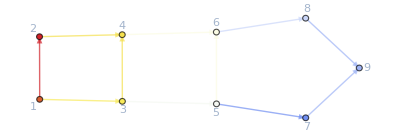

```mathematica
ColorNetworkByValueFunctionOperator[d2ehetero][resulthetero]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming
```

{5.19491,{True,<|j15→2,j16→6,u27→1,u29→2,u30→0,u17→584/41,u2→523/41,u26→0,u28→0,u3→584/41,u4→380/41,u5→380/41,u6→399/41,u7→218/41,u8→218/41,u9→233/41,j11→136/41,j13→69/41,j14→3,j17→61/41,j2→143/41,j24→0,j25→0,j27→0,j29→0,j3→185/41,j30→0,j31→0,j32→0,j4→0,j5→162/41,j6→166/41,j7→0,j8→177/41,j9→151/41,jt1→61/41,jt10→0,jt11→61/41,jt12→185/41,jt14→143/41,jt15→0,jt16→19/41,jt17→0,jt18→0,jt2→0,jt20→166/41,jt21→0,jt22→0,jt23→0,jt24→0,jt26→162/41,jt27→0,jt28→15/41,jt29→0,jt3→0,jt30→0,jt31→15/41,jt32→151/41,jt33→0,jt34→0,jt36→0,jt37→1,jt38→136/41,jt4→0,jt40→0,jt41→0,jt42→0,jt43→2,jt44→69/41,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→1,jt51→0,jt52→2,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→523/41,u11→1,u12→2,u13→2,u14→0,u18→380/41,u19→399/41,u20→399/41,u21→218/41,u22→233/41,u23→233/41,u24→1,u25→2,u31→523/41,u32→584/41,j1→0,j10→1,j12→2,j18→0,j19→0,j20→19/41,j21→0,j22→0,j23→15/41,j26→0,j28→0,jt13→0,jt19→19/41,jt25→0,jt35→0,jt39→0,jt45→0,u10→1,u15→523/41,u16→584/41|>}}

```mathematica
{time1data,d2e1}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time1data
```

0.29791

```mathematica
{time1,{system1,rules1}}=CriticalCongestionSolver[d2e1]//AbsoluteTiming
```

{2.64039,{True,<|j15→2,j16→6,u27→3,u29→3,u30→0.,u17→645/41,u2→585/41,u26→0,u28→0,u3→645/41,u4→443/41,u5→443/41,u6→459/41,u7→285/41,u8→285/41,u9→289/41,j11→39/41,j13→43/41,j14→6,j17→60/41,j2→142/41,j24→0,j25→0,j27→0,j29→0,j3→186/41,j30→0,j31→0,j32→0,j4→0,j5→158/41,j6→170/41,j7→0,j8→162/41,j9→166/41,jt1→60/41,jt10→0,jt11→60/41,jt12→186/41,jt14→142/41,jt15→0,jt16→16/41,jt17→0,jt18→0,jt2→0,jt20→170/41,jt21→0,jt22→0,jt23→0,jt24→0,jt26→158/41,jt27→0,jt28→4/41,jt29→0,jt3→0,jt30→0,jt31→4/41,jt32→166/41,jt33→0,jt34→0,jt36→0,jt37→3,jt38→39/41,jt4→0,jt40→0,jt41→0,jt42→0,jt43→3,jt44→43/41,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→3,jt51→0,jt52→3,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→585/41,u11→3,u12→3,u13→3,u14→0.,u18→443/41,u19→459/41,u20→459/41,u21→285/41,u22→289/41,u23→289/41,u24→3,u25→3,u31→585/41,u32→645/41,j1→0,j10→3,j12→3,j18→0,j19→0,j20→16/41,j21→0,j22→0,j23→4/41,j26→0,j28→0,jt13→0,jt19→16/41,jt25→0,jt35→0,jt39→0,jt45→0,u10→3,u15→585/41,u16→645/41|>}}

#### Non-linear case

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e1;
FFR=rules1;
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@MFGEquations["BEL"];
```

```mathematica
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@MFGEquations["BEL"];
```

```mathematica
Graph[d2e1["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[d2e1["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Keys[d2e1]
```

{Vertices List,Adjacency Matrix,Entrance Vertices and Currents,Exit Vertices and Terminal Costs,Switching Costs,BG,FG,jvars,jtvars,uvars,OutRules,InRules,jays,ExitCosts,AllOr,AllEq,AllIneq,EqAllAll,BoundaryRules,Nlhs,MinimalTimeRhs,EqCriticalCase,Nrhs}

```mathematica
alpha = .1;
Solver[d2e1][alpha]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

The error (1-Norm of LHS-RHS) is 2.16836

The error (1-Norm of LHS-RHS) is 0.483755

The error (1-Norm of LHS-RHS) is 0.390939

The error (1-Norm of LHS-RHS) is 0.316361

The error (1-Norm of LHS-RHS) is 0.256598

It took 37.2153 seconds to solve!
	The system is True

<|u17→6.31702,u2→5.57449,u26→0.,u28→0.,u3→6.31702,u4→4.26463,u5→4.26463,u6→4.67355,u7→2.87157,u8→2.87157,u9→3.09051,j11→0,j13→0,j14→8,j15→2,j16→6,j17→762935256921/710000000000,j2→2182935256921/710000000000,j24→0,j25→0,j27→0,j29→0,j3→3497064743079/710000000000,j30→0,j31→0,j32→0,j4→0,j5→1262002871059/355000000000,j6→1577997128941/355000000000,j7→0,j8→539340377187/142000000000,j9→596659622813/142000000000,jt1→762935256921/710000000000,jt10→0,jt11→762935256921/710000000000,jt12→3497064743079/710000000000,jt14→2182935256921/710000000000,jt15→0,jt16→341070485197/710000000000,jt17→0,jt18→0,jt2→0,jt20→1577997128941/355000000000,jt21→0,jt22→0,jt23→0,jt24→0,jt26→1262002871059/355000000000,jt27→0,jt28→172696143817/710000000000,jt29→0,jt3→0,jt30→0,jt31→172696143817/710000000000,jt32→596659622813/142000000000,jt33→0,jt34→0,jt36→0,jt37→539340377187/142000000000,jt38→0,jt4→0,jt40→0,jt41→0,jt42→0,jt43→596659622813/142000000000,jt44→0,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→539340377187/142000000000,jt51→0,jt52→596659622813/142000000000,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→5.57449,u11→3,u12→1.54525,u13→3,u14→0.,u18→4.26463,u19→4.67355,u20→4.67355,u21→2.87157,u22→3.09051,u23→3.09051,u24→1.43578,u25→1.54525,u27→3,u29→3,u30→0.,u31→5.57449,u32→6.31702,j1→0,j10→539340377187/142000000000,j12→596659622813/142000000000,j18→0,j19→0,j20→341070485197/710000000000,j21→0,j22→0,j23→172696143817/710000000000,j26→0,j28→0,jt13→0,jt19→341070485197/710000000000,jt25→0,jt35→0,jt39→0,jt45→0,u10→1.43578,u15→5.57449,u16→6.31702|>

```mathematica
FFR =%;
```

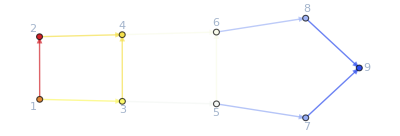

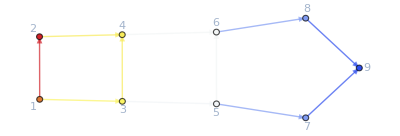

```mathematica
ColorNetworkByValueFunctionOperator[d2e1][FFR]
ColorNetworkByValueFunctionOperator[d2e1][rules1]
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[d2e1["js"],Table[0,{i,1,Length@d2e1["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e1],rules0, 1]
d2e1["EqCriticalCase"]/.FFR
```

```mathematica
d2e=d2ehetero;
rules0=AssociationThread[d2e1["js"],Table[0,{i,1,Length@d2e["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege,U1}/.U1->0},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rulesgrid//KeySort
```

```mathematica
alpha=1;
rulesgridsolver = Solver[d2egrid][alpha];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgridsolver]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data]
```

{0.184324,<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},21,Nrhs→{j1-j35+IntM[j1-j35,1->2],j2-j36+IntM[j2-j36,1->4],j3-j37+IntM[j3-j37,2->3],26,j31-j65+IntM[j31-j65,18->21],j32-j66+IntM[j32-j66,19->20],j33-j67+IntM[j33-j67,20->21]}|>}
 |  |  |  |

```mathematica
d2egrid["EqAllAll"]
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

j1≥0&&j2≥0&&j3≥0&&j1-j2-j3+j37+j38≥0&&j3≥0&&-j1-j11-j12+j2+j40+j45+j46≥0&&j11+j12+j41-j45-j46≥0&&j10-j3+j37+j42-j44≥0&&-j10-j11-j12+j43+j44+j45+j46≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j27≥0&&j33≥0&&j2≥0&&j1≥0&&j37≥0&&j38≥0&&j37≥0&&j40≥0&&j41≥0&&j42≥0&&j43≥0&&j44≥0&&j45≥0&&j46≥0&&j47≥0&&j48≥0&&-j10-j13+j15+j44+j47≥0&&j50≥0&&-j12+j16+j17+j46-j50≥0&&j52≥0&&-j14-j16+j18+j19+j48+j50-j52≥0&&-j10-j13-j18+j20+j44+j47+j52≥0&&j55≥0&&-j12+j16+j21+j22+j46-j50-j55≥0&&j57≥0&&-j14-j16+j18-j21+j23+j24+j48+j50-j52+j55-j57≥0&&-j10-j13-j18-j23+j25+j44+j47+j52+j57≥0&&j60≥0&&-j12+j16+j21+j26+j27+j46-j50-j55-j60≥0&&j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57≥0&&j12-j16-j21-j26+j29+j31-j33-j46+j50+j55+j60≥0&&-j10-j12-j13-j14+j30+j44+j46+j47+j48≥0&&j33≥0&&-j12+j16+j21+j26+j27+j46-j50-j55-j60≥0&&j31≥0&&400-j10-j12-j13-j14+j44+j46+j47+j48≥0&&j2≥0&&j1≥0&&jt3≥0&&j1-jt3≥0&&j2+j3-j38-jt3≥0&&-j2-j3+j37+j38+jt3≥0&&-j3+j38+jt3≥0&&j3-jt3≥0&&j3≥0&&j37≥0&&jt11≥0&&j2-jt11≥0&&-j11-j12+j2+j40-j41+j45+j46-jt11≥0&&j11+j12-j2+j41-j45-j46+jt11≥0&&j1+j11+j12-j2-j40+j41-j45-j46+jt11≥0&&-j1-j11-j12+j2+j40+j45+j46-jt11≥0&&jt17≥0&&jt18≥0&&j1-j2-j3+j37+j38-jt17-jt18≥0&&jt20≥0&&jt21≥0&&-j1-j11-j12+j2+j40+j45+j46-jt20-jt21≥0&&jt23≥0&&j10-j3+j37+j38+j40+j42-j43-j44-jt17-jt18-jt20-jt21-jt23≥0&&-j10+j3-j37-j38-j40+j43+j44+jt17+jt18+jt20+jt21≥0&&j38-jt20-jt23≥0&&-j10+j3-j37-j38-j42+j43+j44+jt18+jt20+jt21+jt23≥0&&j10-j3+j37+j42-j44-jt18-jt21≥0&&jt29≥0&&j3-jt29≥0&&j37+j42-j44-jt29≥0&&j10-j3+jt29≥0&&-j42+j44+jt29≥0&&j42-jt29≥0&&jt35≥0&&j11+j12+j41-j45-j46-jt35≥0&&j11+j41-j46-jt35≥0&&-j11-j41+j45+j46+jt35≥0&&-j11+j46+jt35≥0&&j11-jt35≥0&&jt41≥0&&jt42≥0&&jt43≥0&&-j10-j11-j12+j43+j44+j45+j46-jt41-jt42-jt43≥0&&jt45≥0&&jt46≥0&&jt47≥0&&j11-jt45-jt46-jt47≥0&&jt49≥0&&jt50≥0&&jt51≥0&&j47-jt49-jt50-jt51≥0&&jt53≥0&&jt54≥0&&-400+j13+j14+j43+j45-jt41-jt42-jt43-jt45-jt46-jt47-jt49-jt50-jt51-jt53-jt54≥0&&400-j13-j14-j43-j45+j48+jt41+jt42+jt43+jt45+jt46+jt47+jt49+jt50+jt51≥0&&j43-jt45-jt49-jt53≥0&&j45-jt41-jt50-jt54≥0&&400-j14-j43-j45+jt41+jt43+jt45+jt47+jt49+jt50+jt51+jt53+jt54≥0&&j14-jt43-jt47-jt51≥0&&jt61≥0&&j10-jt61≥0&&j10+j13-j15-jt61≥0&&-j10+j15+jt61≥0&&-j10-j13+j15+j44+jt61≥0&&j47-jt61≥0&&jt67≥0&&j12-jt67≥0&&j12-j17+j50-jt67≥0&&-j12+j17+jt67≥0&&-j12+j17+j46-j50+jt67≥0&&j16-jt67≥0&&jt73≥0&&jt74≥0&&j14-jt73-jt74≥0&&jt76≥0&&jt77≥0&&j16-jt76-jt77≥0&&jt79≥0&&j14+j16-j19+j52-jt73-jt74-jt76-jt77-jt79≥0&&-j14-j16+j19+jt73+jt74+jt76+jt77≥0&&j48-jt76-jt79≥0&&-j14-j16+j19+j50-j52+jt74+jt76+jt77+jt79≥0&&j18-jt74-jt77≥0&&jt85≥0&&j15-jt85≥0&&j15+j18-j20-jt85≥0&&-j15+j20+jt85≥0&&-j10-j13-j18+j20+j44+j47+jt85≥0&&j52-jt85≥0&&jt91≥0&&j17-jt91≥0&&j17-j22+j55-jt91≥0&&-j17+j22+jt91≥0&&-j12+j16+j22+j46-j50-j55+jt91≥0&&j21-jt91≥0&&j55-jt104-jt107≥0&&j19+j21-j24-j55+j57-jt100-jt101-jt103+jt107≥0&&-j21+j24-j57+jt100+jt101+jt103+jt104≥0&&jt100≥0&&jt101≥0&&j21-jt100-jt101≥0&&jt103≥0&&jt104≥0&&j57-jt103-jt104≥0&&-j14-j16+j18+j19+j48+j50-j52-jt100-jt103≥0&&jt107≥0&&-j19-j21+j23+j24+j55-j57+jt100+jt103-jt107≥0&&jt109≥0&&j20-jt109≥0&&j20+j23-j25-jt109≥0&&-j20+j25+jt109≥0&&-j10-j13-j18-j23+j25+j44+j47+j52+jt109≥0&&j57-jt109≥0&&jt115≥0&&j22-jt115≥0&&j22-j27+j60-jt115≥0&&-j22+j27+jt115≥0&&-j12+j16+j21+j27+j46-j50-j55-j60+jt115≥0&&j26-jt115≥0&&jt121≥0&&jt122≥0&&jt123≥0&&j24-jt121-jt122-jt123≥0&&jt125≥0&&jt126≥0&&jt127≥0&&j26-jt125-jt126-jt127≥0&&jt129≥0&&jt130≥0&&jt131≥0&&j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57-jt129-jt130-jt131≥0&&jt133≥0&&jt134≥0&&j10+j12+j13-j16+j18-j21+j23+j24+j28+j29-j30-j44-j46-j47+j50-j52+j55-j57+j60-jt121-jt122-jt123-jt125-jt126-jt127-jt129-jt130-jt131-jt133-jt134≥0&&-j10-j13-j18-j23-j24-j26-j28+j30+j31-j33+j44+j47+j52+j57+jt121+jt122+jt123+jt125+jt126+jt127+jt129+jt130+jt131≥0&&-j14-j16+j18-j21+j23+j24+j48+j50-j52+j55-j57-jt125-jt129-jt133≥0&&j60-jt121-jt130-jt134≥0&&-j10-j12-j13+j16-j18+j21-j23-j24-j29+j30+j44+j46+j47-j50+j52-j55+j57-j60+jt121+jt123+jt125+jt127+jt129+jt130+jt131+jt133+jt134≥0&&j29-jt123-jt127-jt131≥0&&jt141≥0&&j25-jt141≥0&&j25+j28-j31-jt141≥0&&-j25+j31+jt141≥0&&-j10-j13-j18-j23-j28+j31+j44+j47+j52+j57+jt141≥0&&j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57-jt141≥0&&j27≥0&&-j12+j16+j21+j26+j27+j46-j50-j55-j60≥0&&jt149≥0&&j29-jt149≥0&&j27+j29-j33-jt149≥0&&-j29+j33+jt149≥0&&j12-j16-j21-j26-j27+j31-j46+j50+j55+j60+jt149≥0&&-j12+j16+j21+j26+j27+j46-j50-j55-j60-jt149≥0&&j31≥0&&j33≥0&&u1==u2&&-j1+j2+u1==j1-j2-j3+j37+u38&&u3==-j1+j2+u1&&-j3+j37+u3==j3-j37+u39&&-j1-j11-j12+j2+j45+j46+u40==j11+j12-j45-j46+u41&&j1-j2+u2==j11+j12-j45-j46+u41&&u40==-j10-j11-j12+j44+j45+j46+u43&&j10-j3+j37-j44+u42==-j10-j11-j12+j44+j45+j46+u43&&u38==u40&&u39==u42&&u10==u39&&u12==u41&&u11==u41&&-j11+j45+u11≥u34&&u43==-j11+j45+u11&&u14==u43&&u13==-j11+j45+u11&&-j10+j44+u10==-j13+j47+u13&&u15==-j10+j44+u10&&u17==-j12+j46+u12&&u16==-j12+j46+u12&&-j14+j48+u14==-j16+j50+u16&&u19==-j16+j50+u16&&u18==-j16+j50+u16&&-j10-j13+j44+j47+u15==-j18+j52+u18&&u20==-j10-j13+j44+j47+u15&&u22==-j12+j16+j46-j50+u17&&u21==-j12+j16+j46-j50+u17&&-j14-j16+j18+j48+j50-j52+u19==-j21+j55+u21&&u24==-j21+j55+u21&&u23==-j21+j55+u21&&-j10-j13-j18+j44+j47+j52+u20==-j23+j57+u23&&u25==-j10-j13-j18+j44+j47+j52+u20&&u27==-j12+j16+j21+j46-j50-j55+u22&&u26==-j12+j16+j21+j46-j50-j55+u22&&0≥-j26+j60+u26&&-j14-j16+j18-j21+j23+j48+j50-j52+j55-j57+u24==-j26+j60+u26&&u29==-j14-j16+j18-j21+j23+j48+j50-j52+j55-j57+u24&&u28==-j26+j60+u26&&-j10-j13-j18-j23+j44+j47+j52+j57+u25==j10+j13+j18+j23-j31+j33-j44-j47-j52-j57+u28&&u31==-j10-j13-j18-j23+j44+j47+j52+j57+u25&&u32==-j12+j16+j21+j26+j46-j50-j55-j60+u27&&j12-j16-j21-j26+j31-j33-j46+j50+j55+j60+u29==-j12+j16+j21+j26+j46-j50-j55-j60+u32&&u33==j12-j16-j21-j26+j31-j33-j46+j50+j55+j60+u29&&-j31+j33+u31==j31-j33+u33&&(j2==0||j1==0)&&(j1==0||j2==0)&&(j37==0||j3==0)&&(j38==0||j1-j2-j3+j37+j38==0)&&(j37==0||j3==0)&&(j40==0||-j1-j11-j12+j2+j40+j45+j46==0)&&(j41==0||j11+j12+j41-j45-j46==0)&&(j42==0||j10-j3+j37+j42-j44==0)&&(j43==0||-j10-j11-j12+j43+j44+j45+j46==0)&&(j44==0||j10==0)&&(j45==0||j11==0)&&(j46==0||j12==0)&&(j47==0||j13==0)&&(j48==0||j14==0)&&(-j10-j13+j15+j44+j47==0||j15==0)&&(j50==0||j16==0)&&(-j12+j16+j17+j46-j50==0||j17==0)&&(j52==0||j18==0)&&(-j14-j16+j18+j19+j48+j50-j52==0||j19==0)&&(-j10-j13-j18+j20+j44+j47+j52==0||j20==0)&&(j55==0||j21==0)&&(-j12+j16+j21+j22+j46-j50-j55==0||j22==0)&&(j57==0||j23==0)&&(-j14-j16+j18-j21+j23+j24+j48+j50-j52+j55-j57==0||j24==0)&&(-j10-j13-j18-j23+j25+j44+j47+j52+j57==0||j25==0)&&(j60==0||j26==0)&&(-j12+j16+j21+j26+j27+j46-j50-j55-j60==0||j27==0)&&(j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57==0||j28==0)&&(j12-j16-j21-j26+j29+j31-j33-j46+j50+j55+j60==0||j29==0)&&(-j10-j12-j13-j14+j30+j44+j46+j47+j48==0||j30==0)&&(j33==0||j31==0)&&(-j12+j16+j21+j26+j27+j46-j50-j55-j60==0||j27==0)&&(j31==0||j33==0)&&400-j10-j12-j13-j14+j44+j46+j47+j48==0&&(j2==0||j1==0)&&(j37==0||j3==0)&&(jt100==0||j55-jt104-jt107==0)&&(jt101==0||jt104==0)&&(j21-jt100-jt101==0||jt107==0)&&(jt103==0||j19+j21-j24-j55+j57-jt100-jt101-jt103+jt107==0)&&(j57-jt103-jt104==0||-j19-j21+j23+j24+j55-j57+jt100+jt103-jt107==0)&&(-j14-j16+j18+j19+j48+j50-j52-jt100-jt103==0||-j21+j24-j57+jt100+jt101+jt103+jt104==0)&&(jt109==0||j20+j23-j25-jt109==0)&&(jt11==0||-j11-j12+j2+j40-j41+j45+j46-jt11==0)&&(j20-jt109==0||-j10-j13-j18-j23+j25+j44+j47+j52+jt109==0)&&(-j20+j25+jt109==0||j57-jt109==0)&&(jt115==0||j22-j27+j60-jt115==0)&&(j22-jt115==0||-j12+j16+j21+j27+j46-j50-j55-j60+jt115==0)&&(-j22+j27+jt115==0||j26-jt115==0)&&(j2-jt11==0||j1+j11+j12-j2-j40+j41-j45-j46+jt11==0)&&(jt121==0||jt125==0)&&(jt122==0||jt129==0)&&(jt123==0||jt133==0)&&(j24-jt121-jt122-jt123==0||-j14-j16+j18-j21+j23+j24+j48+j50-j52+j55-j57-jt125-jt129-jt133==0)&&(jt126==0||jt130==0)&&(jt127==0||jt134==0)&&(j26-jt125-jt126-jt127==0||j60-jt121-jt130-jt134==0)&&(jt131==0||j10+j12+j13-j16+j18-j21+j23+j24+j28+j29-j30-j44-j46-j47+j50-j52+j55-j57+j60-jt121-jt122-jt123-jt125-jt126-jt127-jt129-jt130-jt131-jt133-jt134==0)&&(j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57-jt129-jt130-jt131==0||-j10-j12-j13+j16-j18+j21-j23-j24-j29+j30+j44+j46+j47-j50+j52-j55+j57-j60+jt121+jt123+jt125+jt127+jt129+jt130+jt131+jt133+jt134==0)&&(-j10-j13-j18-j23-j24-j26-j28+j30+j31-j33+j44+j47+j52+j57+jt121+jt122+jt123+jt125+jt126+jt127+jt129+jt130+jt131==0||j29-jt123-jt127-jt131==0)&&(j11+j12-j2+j41-j45-j46+jt11==0||-j1-j11-j12+j2+j40+j45+j46-jt11==0)&&(jt141==0||j25+j28-j31-jt141==0)&&(j25-jt141==0||-j10-j13-j18-j23-j28+j31+j44+j47+j52+j57+jt141==0)&&(-j25+j31+jt141==0||j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57-jt141==0)&&(j27==0||-j12+j16+j21+j26+j27+j46-j50-j55-j60==0)&&(jt149==0||j27+j29-j33-jt149==0)&&(j29-jt149==0||j12-j16-j21-j26-j27+j31-j46+j50+j55+j60+jt149==0)&&(-j29+j33+jt149==0||-j12+j16+j21+j26+j27+j46-j50-j55-j60-jt149==0)&&(j31==0||j33==0)&&(jt17==0||jt20==0)&&(jt18==0||jt23==0)&&(j1-j2-j3+j37+j38-jt17-jt18==0||j38-jt20-jt23==0)&&(jt21==0||j10-j3+j37+j38+j40+j42-j43-j44-jt17-jt18-jt20-jt21-jt23==0)&&(-j1-j11-j12+j2+j40+j45+j46-jt20-jt21==0||-j10+j3-j37-j38-j42+j43+j44+jt18+jt20+jt21+jt23==0)&&(-j10+j3-j37-j38-j40+j43+j44+jt17+jt18+jt20+jt21==0||j10-j3+j37+j42-j44-jt18-jt21==0)&&(jt29==0||j37+j42-j44-jt29==0)&&(jt3==0||j2+j3-j38-jt3==0)&&(j3-jt29==0||-j42+j44+jt29==0)&&(j10-j3+jt29==0||j42-jt29==0)&&(jt35==0||j11+j41-j46-jt35==0)&&(j11+j12+j41-j45-j46-jt35==0||-j11+j46+jt35==0)&&(-j11-j41+j45+j46+jt35==0||j11-jt35==0)&&(j1-jt3==0||-j3+j38+jt3==0)&&(jt41==0||jt45==0)&&(jt42==0||jt49==0)&&(jt43==0||jt53==0)&&(-j10-j11-j12+j43+j44+j45+j46-jt41-jt42-jt43==0||j43-jt45-jt49-jt53==0)&&(jt46==0||jt50==0)&&(jt47==0||jt54==0)&&(j11-jt45-jt46-jt47==0||j45-jt41-jt50-jt54==0)&&(jt51==0||-400+j13+j14+j43+j45-jt41-jt42-jt43-jt45-jt46-jt47-jt49-jt50-jt51-jt53-jt54==0)&&(j47-jt49-jt50-jt51==0||400-j14-j43-j45+jt41+jt43+jt45+jt47+jt49+jt50+jt51+jt53+jt54==0)&&(400-j13-j14-j43-j45+j48+jt41+jt42+jt43+jt45+jt46+jt47+jt49+jt50+jt51==0||j14-jt43-jt47-jt51==0)&&(-j2-j3+j37+j38+jt3==0||j3-jt3==0)&&(jt61==0||j10+j13-j15-jt61==0)&&(j10-jt61==0||-j10-j13+j15+j44+jt61==0)&&(-j10+j15+jt61==0||j47-jt61==0)&&(jt67==0||j12-j17+j50-jt67==0)&&(j12-jt67==0||-j12+j17+j46-j50+jt67==0)&&(-j12+j17+jt67==0||j16-jt67==0)&&(jt73==0||jt76==0)&&(jt74==0||jt79==0)&&(j14-jt73-jt74==0||j48-jt76-jt79==0)&&(jt77==0||j14+j16-j19+j52-jt73-jt74-jt76-jt77-jt79==0)&&(j16-jt76-jt77==0||-j14-j16+j19+j50-j52+jt74+jt76+jt77+jt79==0)&&(-j14-j16+j19+jt73+jt74+jt76+jt77==0||j18-jt74-jt77==0)&&(jt85==0||j15+j18-j20-jt85==0)&&(j15-jt85==0||-j10-j13-j18+j20+j44+j47+jt85==0)&&(-j15+j20+jt85==0||j52-jt85==0)&&(jt91==0||j17-j22+j55-jt91==0)&&(j17-jt91==0||-j12+j16+j22+j46-j50-j55+jt91==0)&&(-j17+j22+jt91==0||j21-jt91==0)&&(j2==0||-u1+u2==0)&&(j1==0||u1-u2==0)&&(jt3==0||j1-j2-u1+u3==0)&&(j1-jt3==0||2 j1-2 j2-j3+j37-u1+u38==0)&&(j2+j3-j38-jt3==0||-j1+j2+u1-u3==0)&&(-j2-j3+j37+j38+jt3==0||j1-j2-j3+j37-u3+u38==0)&&(-j3+j38+jt3==0||-2 j1+2 j2+j3-j37+u1-u38==0)&&(j3-jt3==0||-j1+j2+j3-j37+u3-u38==0)&&(j3==0||2 j3-2 j37-u3+u39==0)&&(j37==0||-2 j3+2 j37+u3-u39==0)&&(jt11==0||-2 j1-j11-j12+2 j2+j45+j46-u2+u40==0)&&(j2-jt11==0||-j1+j11+j12+j2-j45-j46-u2+u41==0)&&(-j11-j12+j2+j40-j41+j45+j46-jt11==0||2 j1+j11+j12-2 j2-j45-j46+u2-u40==0)&&(j11+j12-j2+j41-j45-j46+jt11==0||j1+2 j11+2 j12-j2-2 j45-2 j46-u40+u41==0)&&(j1+j11+j12-j2-j40+j41-j45-j46+jt11==0||j1-j11-j12-j2+j45+j46+u2-u41==0)&&(-j1-j11-j12+j2+j40+j45+j46-jt11==0||-j1-2 j11-2 j12+j2+2 j45+2 j46+u40-u41==0)&&(jt17==0||-u38+u40==0)&&(jt18==0||j10-j3+j37-j44-u38+u42==0)&&(j1-j2-j3+j37+j38-jt17-jt18==0||-j10-j11-j12+j44+j45+j46-u38+u43==0)&&(jt20==0||u38-u40==0)&&(jt21==0||j10-j3+j37-j44-u40+u42==0)&&(-j1-j11-j12+j2+j40+j45+j46-jt20-jt21==0||-j10-j11-j12+j44+j45+j46-u40+u43==0)&&(jt23==0||-j10+j3-j37+j44+u38-u42==0)&&(j10-j3+j37+j38+j40+j42-j43-j44-jt17-jt18-jt20-jt21-jt23==0||-j10+j3-j37+j44+u40-u42==0)&&(-j10+j3-j37-j38-j40+j43+j44+jt17+jt18+jt20+jt21==0||-2 j10-j11-j12+j3-j37+2 j44+j45+j46-u42+u43==0)&&(j38-jt20-jt23==0||j10+j11+j12-j44-j45-j46+u38-u43==0)&&(-j10+j3-j37-j38-j42+j43+j44+jt18+jt20+jt21+jt23==0||j10+j11+j12-j44-j45-j46+u40-u43==0)&&(j10-j3+j37+j42-j44-jt18-jt21==0||2 j10+j11+j12-j3+j37-2 j44-j45-j46+u42-u43==0)&&(jt29==0||-u39+u42==0)&&(j3-jt29==0||u10-u39==0)&&(j37+j42-j44-jt29==0||u39-u42==0)&&(j10-j3+jt29==0||u10-u42==0)&&(-j42+j44+jt29==0||-u10+u39==0)&&(j42-jt29==0||-u10+u42==0)&&(jt35==0||u11-u41==0)&&(j11+j12+j41-j45-j46-jt35==0||u12-u41==0)&&(j11+j41-j46-jt35==0||-u11+u41==0)&&(-j11-j41+j45+j46+jt35==0||-u11+u12==0)&&(-j11+j46+jt35==0||-u12+u41==0)&&(j11-jt35==0||u11-u12==0)&&(jt41==0||-j11+j45+u11-u43==0)&&(jt42==0||u13-u43==0)&&(jt43==0||u14-u43==0)&&-j10-j11-j12+j43+j44+j45+j46-jt41-jt42-jt43==0&&(jt45==0||j11-j45-u11+u43==0)&&(jt46==0||j11-j45-u11+u13==0)&&(jt47==0||j11-j45-u11+u14==0)&&j11-jt45-jt46-jt47==0&&(jt49==0||-u13+u43==0)&&(jt50==0||-j11+j45+u11-u13==0)&&(jt51==0||-u13+u14==0)&&j47-jt49-jt50-jt51==0&&(jt53==0||-u14+u43==0)&&(jt54==0||-j11+j45+u11-u14==0)&&(-400+j13+j14+j43+j45-jt41-jt42-jt43-jt45-jt46-jt47-jt49-jt50-jt51-jt53-jt54==0||u13-u14==0)&&400-j13-j14-j43-j45+j48+jt41+jt42+jt43+jt45+jt46+jt47+jt49+jt50+jt51==0&&(j43-jt45-jt49-jt53==0||-u34+u43==0)&&(j45-jt41-jt50-jt54==0||-j11+j45+u11-u34==0)&&(400-j14-j43-j45+jt41+jt43+jt45+jt47+jt49+jt50+jt51+jt53+jt54==0||u13-u34==0)&&(j14-jt43-jt47-jt51==0||u14-u34==0)&&(jt61==0||j10-j13-j44+j47-u10+u13==0)&&(j10-jt61==0||j10-j44-u10+u15==0)&&(j10+j13-j15-jt61==0||-j10+j13+j44-j47+u10-u13==0)&&(-j10+j15+jt61==0||j13-j47-u13+u15==0)&&(-j10-j13+j15+j44+jt61==0||-j10+j44+u10-u15==0)&&(j47-jt61==0||-j13+j47+u13-u15==0)&&(jt67==0||j12-j46-u12+u16==0)&&(j12-jt67==0||j12-j46-u12+u17==0)&&(j12-j17+j50-jt67==0||-j12+j46+u12-u16==0)&&(-j12+j17+jt67==0||-u16+u17==0)&&(-j12+j17+j46-j50+jt67==0||-j12+j46+u12-u17==0)&&(j16-jt67==0||u16-u17==0)&&(jt73==0||j14-j16-j48+j50-u14+u16==0)&&(jt74==0||j14-j48-u14+u18==0)&&(j14-jt73-jt74==0||j14-j48-u14+u19==0)&&(jt76==0||-j14+j16+j48-j50+u14-u16==0)&&(jt77==0||j16-j50-u16+u18==0)&&(j16-jt76-jt77==0||j16-j50-u16+u19==0)&&(jt79==0||-j14+j48+u14-u18==0)&&(j14+j16-j19+j52-jt73-jt74-jt76-jt77-jt79==0||-j16+j50+u16-u18==0)&&(-j14-j16+j19+jt73+jt74+jt76+jt77==0||-u18+u19==0)&&(j48-jt76-jt79==0||-j14+j48+u14-u19==0)&&(-j14-j16+j19+j50-j52+jt74+jt76+jt77+jt79==0||-j16+j50+u16-u19==0)&&(j18-jt74-jt77==0||u18-u19==0)&&(jt85==0||j10+j13-j18-j44-j47+j52-u15+u18==0)&&(j15-jt85==0||j10+j13-j44-j47-u15+u20==0)&&(j15+j18-j20-jt85==0||-j10-j13+j18+j44+j47-j52+u15-u18==0)&&(-j15+j20+jt85==0||j18-j52-u18+u20==0)&&(-j10-j13-j18+j20+j44+j47+jt85==0||-j10-j13+j44+j47+u15-u20==0)&&(j52-jt85==0||-j18+j52+u18-u20==0)&&(jt91==0||j12-j16-j46+j50-u17+u21==0)&&(j17-jt91==0||j12-j16-j46+j50-u17+u22==0)&&(j17-j22+j55-jt91==0||-j12+j16+j46-j50+u17-u21==0)&&(-j17+j22+jt91==0||-u21+u22==0)&&(-j12+j16+j22+j46-j50-j55+jt91==0||-j12+j16+j46-j50+u17-u22==0)&&(j21-jt91==0||u21-u22==0)&&(j55-jt104-jt107==0||j14+j16-j18-j21-j48-j50+j52+j55-u19+u21==0)&&(j19+j21-j24-j55+j57-jt100-jt101-jt103+jt107==0||j14+j16-j18-j48-j50+j52-u19+u23==0)&&(-j21+j24-j57+jt100+jt101+jt103+jt104==0||j14+j16-j18-j48-j50+j52-u19+u24==0)&&(jt100==0||-j14-j16+j18+j21+j48+j50-j52-j55+u19-u21==0)&&(jt101==0||j21-j55-u21+u23==0)&&(j21-jt100-jt101==0||j21-j55-u21+u24==0)&&(jt103==0||-j14-j16+j18+j48+j50-j52+u19-u23==0)&&(jt104==0||-j21+j55+u21-u23==0)&&(j57-jt103-jt104==0||-u23+u24==0)&&(-j14-j16+j18+j19+j48+j50-j52-jt100-jt103==0||-j14-j16+j18+j48+j50-j52+u19-u24==0)&&(jt107==0||-j21+j55+u21-u24==0)&&(-j19-j21+j23+j24+j55-j57+jt100+jt103-jt107==0||u23-u24==0)&&(jt109==0||j10+j13+j18-j23-j44-j47-j52+j57-u20+u23==0)&&(j20-jt109==0||j10+j13+j18-j44-j47-j52-u20+u25==0)&&(j20+j23-j25-jt109==0||-j10-j13-j18+j23+j44+j47+j52-j57+u20-u23==0)&&(-j20+j25+jt109==0||j23-j57-u23+u25==0)&&(-j10-j13-j18-j23+j25+j44+j47+j52+jt109==0||-j10-j13-j18+j44+j47+j52+u20-u25==0)&&(j57-jt109==0||-j23+j57+u23-u25==0)&&(jt115==0||j12-j16-j21-j46+j50+j55-u22+u26==0)&&(j22-jt115==0||j12-j16-j21-j46+j50+j55-u22+u27==0)&&(j22-j27+j60-jt115==0||-j12+j16+j21+j46-j50-j55+u22-u26==0)&&(-j22+j27+jt115==0||-u26+u27==0)&&(-j12+j16+j21+j27+j46-j50-j55-j60+jt115==0||-j12+j16+j21+j46-j50-j55+u22-u27==0)&&(j26-jt115==0||u26-u27==0)&&(jt121==0||j14+j16-j18+j21-j23-j26-j48-j50+j52-j55+j57+j60-u24+u26==0)&&(jt122==0||j14+j16-j18+j21-j23-j48-j50+j52-j55+j57-u24+u28==0)&&(jt123==0||j14+j16-j18+j21-j23-j48-j50+j52-j55+j57-u24+u29==0)&&(j24-jt121-jt122-jt123==0||j14+j16-j18+j21-j23-j48-j50+j52-j55+j57-u24==0)&&(jt125==0||-j14-j16+j18-j21+j23+j26+j48+j50-j52+j55-j57-j60+u24-u26==0)&&(jt126==0||j26-j60-u26+u28==0)&&(jt127==0||j26-j60-u26+u29==0)&&(j26-jt125-jt126-jt127==0||j26-j60-u26==0)&&(jt129==0||-j14-j16+j18-j21+j23+j48+j50-j52+j55-j57+u24-u28==0)&&(jt130==0||-j26+j60+u26-u28==0)&&(jt131==0||-u28+u29==0)&&(j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57-jt129-jt130-jt131==0||-u28==0)&&(jt133==0||-j14-j16+j18-j21+j23+j48+j50-j52+j55-j57+u24-u29==0)&&(jt134==0||-j26+j60+u26-u29==0)&&(j10+j12+j13-j16+j18-j21+j23+j24+j28+j29-j30-j44-j46-j47+j50-j52+j55-j57+j60-jt121-jt122-jt123-jt125-jt126-jt127-jt129-jt130-jt131-jt133-jt134==0||u28-u29==0)&&(-j10-j13-j18-j23-j24-j26-j28+j30+j31-j33+j44+j47+j52+j57+jt121+jt122+jt123+jt125+jt126+jt127+jt129+jt130+jt131==0||-u29==0)&&-j14-j16+j18-j21+j23+j24+j48+j50-j52+j55-j57-jt125-jt129-jt133==0&&j60-jt121-jt130-jt134==0&&-j10-j12-j13+j16-j18+j21-j23-j24-j29+j30+j44+j46+j47-j50+j52-j55+j57-j60+jt121+jt123+jt125+jt127+jt129+jt130+jt131+jt133+jt134==0&&j29-jt123-jt127-jt131==0&&(jt141==0||2 j10+2 j13+2 j18+2 j23-j31+j33-2 j44-2 j47-2 j52-2 j57-u25+u28==0)&&(j25-jt141==0||j10+j13+j18+j23-j44-j47-j52-j57-u25+u31==0)&&(j25+j28-j31-jt141==0||-2 j10-2 j13-2 j18-2 j23+j31-j33+2 j44+2 j47+2 j52+2 j57+u25-u28==0)&&(-j25+j31+jt141==0||-j10-j13-j18-j23+j31-j33+j44+j47+j52+j57-u28+u31==0)&&(-j10-j13-j18-j23-j28+j31+j44+j47+j52+j57+jt141==0||-j10-j13-j18-j23+j44+j47+j52+j57+u25-u31==0)&&(j10+j13+j18+j23+j28-j31+j33-j44-j47-j52-j57-jt141==0||j10+j13+j18+j23-j31+j33-j44-j47-j52-j57+u28-u31==0)&&(j27==0||j12-j16-j21-j26-j46+j50+j55+j60-u27+u32==0)&&(-j12+j16+j21+j26+j27+j46-j50-j55-j60==0||-j12+j16+j21+j26+j46-j50-j55-j60+u27-u32==0)&&(jt149==0||-2 j12+2 j16+2 j21+2 j26-j31+j33+2 j46-2 j50-2 j55-2 j60-u29+u32==0)&&(j29-jt149==0||-j12+j16+j21+j26-j31+j33+j46-j50-j55-j60-u29+u33==0)&&(j27+j29-j33-jt149==0||2 j12-2 j16-2 j21-2 j26+j31-j33-2 j46+2 j50+2 j55+2 j60+u29-u32==0)&&(-j29+j33+jt149==0||j12-j16-j21-j26-j46+j50+j55+j60-u32+u33==0)&&(j12-j16-j21-j26-j27+j31-j46+j50+j55+j60+jt149==0||j12-j16-j21-j26+j31-j33-j46+j50+j55+j60+u29-u33==0)&&(-j12+j16+j21+j26+j27+j46-j50-j55-j60-jt149==0||-j12+j16+j21+j26+j46-j50-j55-j60+u32-u33==0)&&(j31==0||2 j31-2 j33-u31+u33==0)&&(j33==0||-2 j31+2 j33+u31-u33==0)

$Aborted

timegrid

-Graphics-

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=AbsoluteTiming@CriticalCongestionSolver[d2egrid];
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rulesgrid=KeySort@rulesgrid;
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rules0=AssociationThread[d2egrid["js"],Table[0,{i,1,Length@d2egrid["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2egrid],rules0, 1]
d2egrid["EqCriticalCase"]/.FFR
```

```mathematica
Solver[d2egrid][1]
```

```mathematica
1650.373971/60
```

```mathematica
$IterationLimit
```